```mathematica
e[k2_,t1_,t2_,a_,z_]:=2t1 Cos[a k2]+2 t2 Cos[2 a k2] +z Sqrt[t1^2+t2^2+2t1 t2 Cos[a k2]]
```

```mathematica
e[k2_,t1_,t2_,z_]:=2(t1+t2)(1+2Cos[k2]+2 Cos[2 k2]) +z Sqrt[t1^2+t2^2+2t1 t2 Cos[ k2]]
```

```mathematica
Manipulate[Plot[{e[k2,t1,t2,+1],e[k2,t1,t2,-1]},{k2,-15,15}],{t1,-2,2},{t2,-2,2}]
```

```mathematica
a1=D[e[k2,t1,t2,1],k2]
```

-(t1 t2 Sin[k2])/(√(t1^2+t2^2+2 t1 t2 Cos[k2]))+2 (t1+t2) (-2 Sin[k2]-4 Sin[2 k2])

```mathematica
a2=D[e[k2,t1,t2,1],{k2,2}]
```

-(t1 t2 Cos[k2])/(√(t1^2+t2^2+2 t1 t2 Cos[k2]))+2 (t1+t2) (-2 Cos[k2]-8 Cos[2 k2])-(t1^2 t2^2 Sin[k2]^2)/((t1^2+t2^2+2 t1 t2 Cos[k2])^(3/2))

```mathematica
Solve[a1==0,k2]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k2→0},{k2→-ArcCos[-(t1^4+3 t1^3 t2+4 t1^2 t2^2+3 t1 t2^3+t2^4)/(6 t1 t2 (t1^2+2 t1 t2+t2^2))-(-65536 t1^8-196608 t1^7 t2-278528 t1^6 t2^2-393216 t1^5 t2^3-491520 t1^4 t2^4-393216 t1^3 t2^5-278528 t1^2 t2^6-196608 t1 t2^7-65536 t2^8)/(49152 2^(2/3) t1 t2 (t1^2+2 t1 t2+t2^2) (-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3))+(-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3)/(24 2^(1/3) t1 t2 (t1^2+2 t1 t2+t2^2))]},{k2→ArcCos[-(t1^4+3 t1^3 t2+4 t1^2 t2^2+3 t1 t2^3+t2^4)/(6 t1 t2 (t1^2+2 t1 t2+t2^2))-(-65536 t1^8-196608 t1^7 t2-278528 t1^6 t2^2-393216 t1^5 t2^3-491520 t1^4 t2^4-393216 t1^3 t2^5-278528 t1^2 t2^6-196608 t1 t2^7-65536 t2^8)/(49152 2^(2/3) t1 t2 (t1^2+2 t1 t2+t2^2) (-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3))+(-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3)/(24 2^(1/3) t1 t2 (t1^2+2 t1 t2+t2^2))]},{k2→-ArcCos[-(t1^4+3 t1^3 t2+4 t1^2 t2^2+3 t1 t2^3+t2^4)/(6 t1 t2 (t1^2+2 t1 t2+t2^2))+((1+ⅈ √3) (-65536 t1^8-196608 t1^7 t2-278528 t1^6 t2^2-393216 t1^5 t2^3-491520 t1^4 t2^4-393216 t1^3 t2^5-278528 t1^2 t2^6-196608 t1 t2^7-65536 t2^8))/(98304 2^(2/3) t1 t2 (t1^2+2 t1 t2+t2^2) (-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3))-((1-ⅈ √3) (-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3))/(48 2^(1/3) t1 t2 (t1^2+2 t1 t2+t2^2))]},{k2→ArcCos[-(t1^4+3 t1^3 t2+4 t1^2 t2^2+3 t1 t2^3+t2^4)/(6 t1 t2 (t1^2+2 t1 t2+t2^2))+((1+ⅈ √3) (-65536 t1^8-196608 t1^7 t2-278528 t1^6 t2^2-393216 t1^5 t2^3-491520 t1^4 t2^4-393216 t1^3 t2^5-278528 t1^2 t2^6-196608 t1 t2^7-65536 t2^8))/(98304 2^(2/3) t1 t2 (t1^2+2 t1 t2+t2^2) (-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3))-((1-ⅈ √3) (-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3))/(48 2^(1/3) t1 t2 (t1^2+2 t1 t2+t2^2))]},{k2→-ArcCos[-(t1^4+3 t1^3 t2+4 t1^2 t2^2+3 t1 t2^3+t2^4)/(6 t1 t2 (t1^2+2 t1 t2+t2^2))+((1-ⅈ √3) (-65536 t1^8-196608 t1^7 t2-278528 t1^6 t2^2-393216 t1^5 t2^3-491520 t1^4 t2^4-393216 t1^3 t2^5-278528 t1^2 t2^6-196608 t1 t2^7-65536 t2^8))/(98304 2^(2/3) t1 t2 (t1^2+2 t1 t2+t2^2) (-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3))-((1+ⅈ √3) (-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3))/(48 2^(1/3) t1 t2 (t1^2+2 t1 t2+t2^2))]},{k2→ArcCos[-(t1^4+3 t1^3 t2+4 t1^2 t2^2+3 t1 t2^3+t2^4)/(6 t1 t2 (t1^2+2 t1 t2+t2^2))+((1-ⅈ √3) (-65536 t1^8-196608 t1^7 t2-278528 t1^6 t2^2-393216 t1^5 t2^3-491520 t1^4 t2^4-393216 t1^3 t2^5-278528 t1^2 t2^6-196608 t1 t2^7-65536 t2^8))/(98304 2^(2/3) t1 t2 (t1^2+2 t1 t2+t2^2) (-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3))-((1+ⅈ √3) (-128 t1^12-576 t1^11 t2-1248 t1^10 t2^2-2160 t1^9 t2^3-3333 t1^8 t2^4-4068 t1^7 t2^5-4190 t1^6 t2^6-4068 t1^5 t2^7-3333 t1^4 t2^8-2160 t1^3 t2^9-1248 t1^2 t2^10-576 t1 t2^11-128 t2^12+3 √3 √(-256 t1^20 t2^4-2176 t1^19 t2^5-8640 t1^18 t2^6-22240 t1^17 t2^7-43813 t1^16 t2^8-72072 t1^15 t2^9-101452 t1^14 t2^10-122968 t1^13 t2^11-130590 t1^12 t2^12-122968 t1^11 t2^13-101452 t1^10 t2^14-72072 t1^9 t2^15-43813 t1^8 t2^16-22240 t1^7 t2^17-8640 t1^6 t2^18-2176 t1^5 t2^19-256 t1^4 t2^20))^(1/3))/(48 2^(1/3) t1 t2 (t1^2+2 t1 t2+t2^2))]}}

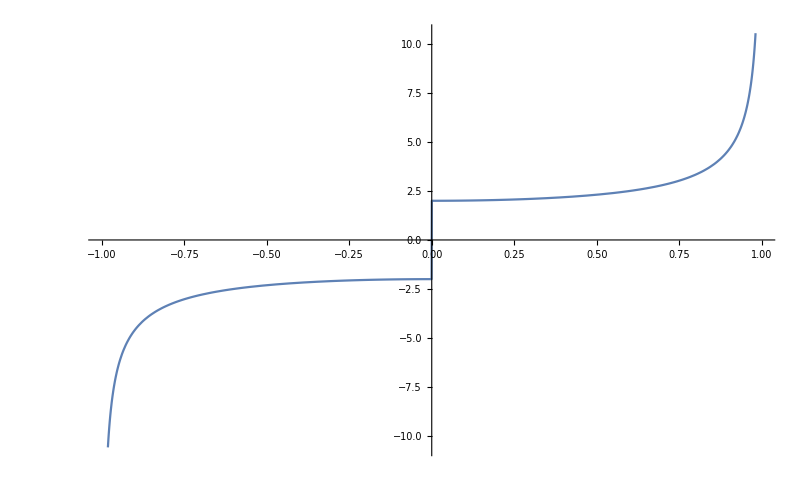

```mathematica
Plot[4Sqrt[1/2+1/2(2 e^2-1)]/(2 e Sqrt[1-e^2]),{e,-1,1}]
```